```mathematica
Needs["VariationalMethods`"]
```

EulerEquations::shdw: Symbol EulerEquations appears in multiple contexts {VariationalMethods`,Global`}; definitions in context VariationalMethods` may shadow or be shadowed by other definitions.

```mathematica
Block[
{f,r,l},
f[r_,l_]:=1+r^2/l^2;
EulerEquations[q/r[t]-Sqrt[-r'[t]^2/f[r[t],l]+f[r[t],l]],r[t],t]
]
```

(2 l^2 r[t]^5+r[t]^7+l^4 r[t]^3 (1-3 r'[t]^2)-l^6 q (-1+r'[t]^2) √((l^4+2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4+l^2 r[t]^2))+r[t]^4 (l^2 q √((l^4+2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4+l^2 r[t]^2))+l^4 r''[t])+r[t]^2 (2 l^4 q √((l^4+2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4+l^2 r[t]^2))+l^6 r''[t]))/(l^2 r[t]^2 √(1+r[t]^2/l^2-(l^2 r'[t]^2)/(l^2+r[t]^2)) (-2 l^2 r[t]^2-r[t]^4+l^4 (-1+r'[t]^2)))==0

```mathematica
(* Empty AdS plots for a neutral particle *)
```

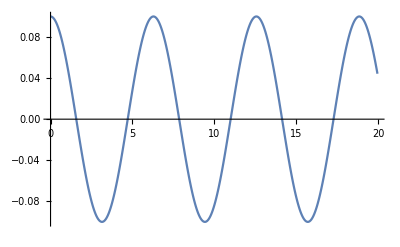

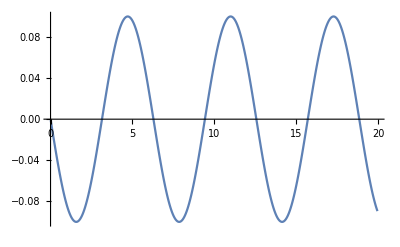

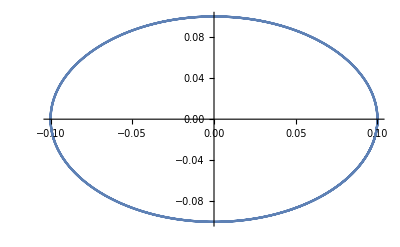

```mathematica
Block[
{dr,f,fr,r,l,rm,pr,t,q,qcrit},
f[r_,l_]:=1+r^2/l^2;
rm[l1_,r1_,q1_]:=NDSolveValue[{2 l^2 r[t]^5+r[t]^7+l^4 r[t]^3 (1-3 r'[t]^2)-l^6 q (-1+r'[t]^2) √((l^4+2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4+l^2 r[t]^2))+r[t]^4 (l^2 q √((l^4+2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4+l^2 r[t]^2))+l^4 r''[t])+r[t]^2 (2 l^4 q √((l^4+2 l^2 r[t]^2+r[t]^4-l^4 r'[t]^2)/(l^4+l^2 r[t]^2))+l^6 r''[t])==0/.{l->l1,q->q1},r[0]==r1,r'[0]==0},r,{t,0.01,20}, Method->"BDF"];
qcrit[l1_,rs_]:=rs Sqrt[f[rs,l1]];
fr[l1_,r1_,t1_,q1_]:=rm[l1,r1,q1][t1];
dr[l1_,r1_,t1_,q1_]:=D[rm[l1,r1,q1][t],t]/.{t->t1};
pr[l1_,r1_,t1_,q1_]:=dr[l1,r1,t1,q1]/Sqrt[-dr[l1,r1,t1,q1]^2f[fr[l1,r1,t1,q1],l1]+f[fr[l1,r1,t1,q1],l1]^3];
Print[ListLinePlot[Table[{i,fr[1,0.1,i,0]},{i,0.01,20,0.05}],AxesOrigin->{0,0}]];
Print[ListLinePlot[Table[{i,pr[1,0.1,i,0]},{i,0.01,20,0.05}],AxesOrigin->{0,0}]];
Print[ListLinePlot[Table[{fr[1,0.1,i,0],pr[1,0.1,i,0]},{i,0.01,20,0.05}],AxesOrigin->{0,0}]];
]
```

```mathematica
(* Schwarzschild AdS plots for a neutral particle *)
```

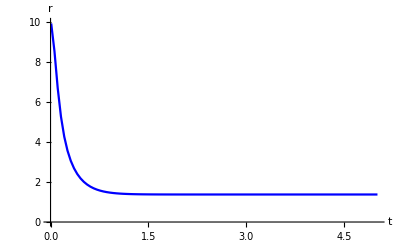

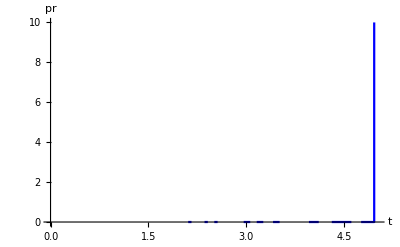

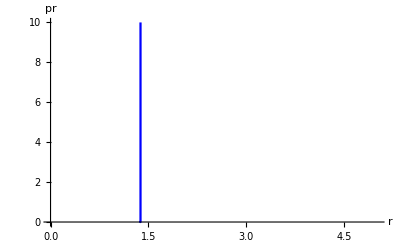

```mathematica
Block[
{dr,f,fr,r,l,rm,pr,t,q,qcrit,M},
f[r1_,M1_,l1_]:=1-2M1/r1+r1^2/l1^2;
rm[l1_,r1_,q1_,M1_]:=NDSolveValue[{(4 l^6 M^3-4 l^6 M^2 r[t]+l^6 M r[t]^2-2 l^4 M r[t]^4+l^4 r[t]^5-3 l^2 M r[t]^6+2 l^2 r[t]^7+r[t]^9-3 l^6 M r[t]^2 r'[t]^2-3 l^4 r[t]^5 r'[t]^2-2 l^6 M q r[t] (1-(2 M)/r[t]+r[t]^2/l^2-r'[t]^2/(1-(2 M)/r[t]+r[t]^2/l^2))^(3/2)+l^6 q r[t]^2 (1-(2 M)/r[t]+r[t]^2/l^2-r'[t]^2/(1-(2 M)/r[t]+r[t]^2/l^2))^(3/2)+l^4 q r[t]^4 (1-(2 M)/r[t]+r[t]^2/l^2-r'[t]^2/(1-(2 M)/r[t]+r[t]^2/l^2))^(3/2)-2 l^6 M r[t]^3 r''[t]+l^6 r[t]^4 r''[t]+l^4 r[t]^6 r''[t])==0/.{l->l1,q->q1,M->M1},r[0]==r1,r'[0]==0},r,{t,0.01,5.01}];
qcrit[rs_,l1_,M1_]:=rs Sqrt[f[rs,M1,l1]];
fr[l1_,r1_,t1_,q1_,M1_]:=rm[l1,r1,q1,M1][t1];
dr[l1_,r1_,t1_,q1_,M1_]:=D[rm[l1,r1,q1,M1][t],t]/.{t->t1};
pr[l1_,r1_,t1_,q1_,M1_]:=dr[l1,r1,t1,q1,M1]/Sqrt[-dr[l1,r1,t1,q1,M1]^2f[fr[l1,r1,t1,q1,M1],M1,l1]+f[fr[l1,r1,t1,q1,M1],M1,l1]^3];
Print[
ListLinePlot[Table[{i,fr[1,10,i,0,2]//Re},{i,0.01,5.01,0.05}],PlotStyle->Blue,AxesLabel->{t,r},AxesOrigin->{0,0},PlotRange->{{0,5.01},{0,10}}]
];
Print[
ListLinePlot[Table[{i,pr[1,10,i,0,2]//Re},{i,0.01,5.01,0.05}],PlotStyle->Blue,AxesLabel->{t,pr},AxesOrigin->{0,0},PlotRange->{{0,5.01},{0,10}}]
];
Print[
ListLinePlot[Table[{fr[1,10,i,0,2]//Re,pr[1,10,i,0,2]//Re},{i,0.01,5.01,0.05}],PlotStyle->Blue,AxesLabel->{r,pr},AxesOrigin->{0,0},PlotRange->{{0,5.01},{0,10}}]
]
]
```

```mathematica
Block[
{dr,f,fr,r,l,rm,pr,t,q,qcrit,M},
f[r1_,M1_,l1_]:=1-2M1/r1+r1^2/l1^2;
rm[l1_,r1_,q1_,M1_]:=NDSolveValue[{(4 l^6 M^3-4 l^6 M^2 r[t]+l^6 M r[t]^2-2 l^4 M r[t]^4+l^4 r[t]^5-3 l^2 M r[t]^6+2 l^2 r[t]^7+r[t]^9-3 l^6 M r[t]^2 r'[t]^2-3 l^4 r[t]^5 r'[t]^2-2 l^6 M q r[t] (1-(2 M)/r[t]+r[t]^2/l^2-r'[t]^2/(1-(2 M)/r[t]+r[t]^2/l^2))^(3/2)+l^6 q r[t]^2 (1-(2 M)/r[t]+r[t]^2/l^2-r'[t]^2/(1-(2 M)/r[t]+r[t]^2/l^2))^(3/2)+l^4 q r[t]^4 (1-(2 M)/r[t]+r[t]^2/l^2-r'[t]^2/(1-(2 M)/r[t]+r[t]^2/l^2))^(3/2)-2 l^6 M r[t]^3 r''[t]+l^6 r[t]^4 r''[t]+l^4 r[t]^6 r''[t])==0/.{l->l1,q->q1,M->M1},r[0]==r1,r'[0]==0},r,{t,0.01,5.01},Method->"Adams"];
qcrit[rs_,l1_,M1_]:=rs Sqrt[f[rs,M1,l1]];
fr[l1_,r1_,t1_,q1_,M1_]:=rm[l1,r1,q1,M1][t1];
dr[l1_,r1_,t1_,q1_,M1_]:=D[rm[l1,r1,q1,M1][t],t]/.{t->t1};
pr[l1_,r1_,t1_,q1_,M1_]:=dr[l1,r1,t1,q1,M1]/Sqrt[-dr[l1,r1,t1,q1,M1]^2f[fr[l1,r1,t1,q1,M1],M1,l1]+f[fr[l1,r1,t1,q1,M1],M1,l1]^3];
Print[" Values of r vs t "];
Print[Table[{i,fr[1,10,i,0,2]},{i,0.01,5.01,0.05}]];
Print[" Values of pr vs t "];
Print[Table[{i,pr[1,10,i,0,2]},{i,0.01,5.01,0.05}]];
Print[" Values of phase space plot "];
Print[Table[{fr[1,10,i,0,2],pr[1,10,i,0,2]},{i,0.01,5.01,0.05}]]
]
```

Values of r vs t

{{0.01,9.94998},{0.06,8.56464},{0.11,6.70649},{0.16,5.27585},{0.21,4.27703},{0.26,3.57457},{0.31,3.06688},{0.36,2.69012},{0.41,2.40455},{0.46,2.18468},{0.51,2.01353},{0.56,1.87935},{0.61,1.77368},{0.66,1.69026},{0.71,1.62435},{0.76,1.57227},{0.81,1.53114},{0.86,1.49867},{0.91,1.47307},{0.96,1.4529},{1.01,1.43702},{1.06,1.42452},{1.11,1.4147},{1.16,1.40698},{1.21,1.40091},{1.26,1.39615},{1.31,1.39241},{1.36,1.38948},{1.41,1.38718},{1.46,1.38537},{1.51,1.38395},{1.56,1.38284},{1.61,1.38197},{1.66,1.38128},{1.71,1.38075},{1.76,1.38033},{1.81,1.38},{1.86,1.37974},{1.91,1.37953},{1.96,1.37938},{2.01,1.37925},{2.06,1.37915},{2.11,1.37908},{2.16,1.37902},{2.21,1.37897},{2.26,1.37893},{2.31,1.3789},{2.36,1.37888},{2.41,1.37886},{2.46,1.37885},{2.51,1.37884},{2.56,1.37883},{2.61,1.37882},{2.66,1.37882},{2.71,1.37881},{2.76,1.37881},{2.81,1.37881},{2.86,1.3788},{2.91,1.3788},{2.96,1.3788},{3.01,1.3788},{3.06,1.3788},{3.11,1.3788},{3.16,1.3788},{3.21,1.3788},{3.26,1.3788},{3.31,1.3788},{3.36,1.3788},{3.41,1.3788},{3.46,1.3788},{3.51,1.3788},{3.56,1.3788},{3.61,1.3788},{3.66,1.3788},{3.71,1.3788},{3.76,1.3788},{3.81,1.3788},{3.86,1.3788},{3.91,1.3788},{3.96,1.3788},{4.01,1.3788},{4.06,1.3788},{4.11,1.3788},{4.16,1.3788},{4.21,1.3788},{4.26,1.3788},{4.31,1.3788},{4.36,1.3788},{4.41,1.3788},{4.46,1.3788},{4.51,1.3788},{4.56,1.3788},{4.61,1.3788},{4.66,1.3788},{4.71,1.3788},{4.76,1.3788},{4.81,1.3788},{4.86,1.3788},{4.91,1.3788},{4.96,1.3788},{5.01,1.3788}}

Values of pr vs t

{{0.01,-0.0100401},{0.06,-0.0699531},{0.11,-0.163748},{0.16,-0.303317},{0.21,-0.494001},{0.26,-0.740822},{0.31,-1.05098},{0.36,-1.43524},{0.41,-1.9091},{0.46,-2.49409},{0.51,-3.21923},{0.56,-4.12283},{0.61,-5.25476},{0.66,-6.67929},{0.71,-8.47881},{0.76,-10.7587},{0.81,-13.6532},{0.86,-17.3334},{0.91,-22.0175},{0.96,-27.9828},{1.01,-35.5836},{1.06,-45.2713},{1.11,-57.6213},{1.16,-73.3674},{1.21,-93.4444},{1.26,-119.042},{1.31,-151.718},{1.36,-193.354},{1.41,-246.821},{1.46,-313.99},{1.51,-400.034},{1.56,-509.812},{1.61,-650.612},{1.66,-828.931},{1.71,-1058.89},{1.76,-1349.74},{1.81,-1716.53},{1.86,-2183.19},{1.91,-2600.25},{1.96,-3542.95},{2.01,-4169.65},{2.06,-4595.36},{2.11,0.+5629.55 ⅈ},{2.16,0.+12818.1 ⅈ},{2.21,-6501.51},{2.26,0.+11224.3 ⅈ},{2.31,-11720.5},{2.36,0.+137123. ⅈ},{2.41,0.+19059.3 ⅈ},{2.46,-26318.},{2.51,0.+42320.1 ⅈ},{2.56,0.+11915.2 ⅈ},{2.61,-8687.64},{2.66,-8349.81},{2.71,-22440.8},{2.76,-29891.1},{2.81,-80045.5},{2.86,-92432.2},{2.91,-10238.7},{2.96,0.+22454.4 ⅈ},{3.01,0.+85091.8 ⅈ},{3.06,0.+21605.4 ⅈ},{3.11,-40204.7},{3.16,0.+33172.3 ⅈ},{3.21,0.+56357.6 ⅈ},{3.26,0.+27570.1 ⅈ},{3.31,-23873.6},{3.36,-35277.3},{3.41,0.+8816.38 ⅈ},{3.46,0.+35752.4 ⅈ},{3.51,0.+21170.7 ⅈ},{3.56,-58830.2},{3.61,-11641.2},{3.66,-43917.8},{3.71,-27555.7},{3.76,-15575.8},{3.81,-16684.4},{3.86,-15931.},{3.91,-15275.9},{3.96,0.+15564.2 ⅈ},{4.01,0.+15109.6 ⅈ},{4.06,0.+55008.4 ⅈ},{4.11,0.+17516.8 ⅈ},{4.16,-13011.3},{4.21,0.+28714.6 ⅈ},{4.26,-48814.7},{4.31,0.+12069.4 ⅈ},{4.36,0.+32746.4 ⅈ},{4.41,-189336.},{4.46,-21545.7},{4.51,-25944.9},{4.56,-32301.},{4.61,-49186.6},{4.66,0.+114941. ⅈ},{4.71,-193629.},{4.76,0.+54364.7 ⅈ},{4.81,0.+46866.8 ⅈ},{4.86,0.+35036.5 ⅈ},{4.91,0.+39335.8 ⅈ},{4.96,0.+39109.9 ⅈ},{5.01,0.+70924.8 ⅈ}}

Values of phase space plot

{{9.94998,-0.0100401},{8.56464,-0.0699531},{6.70649,-0.163748},{5.27585,-0.303317},{4.27703,-0.494001},{3.57457,-0.740822},{3.06688,-1.05098},{2.69012,-1.43524},{2.40455,-1.9091},{2.18468,-2.49409},{2.01353,-3.21923},{1.87935,-4.12283},{1.77368,-5.25476},{1.69026,-6.67929},{1.62435,-8.47881},{1.57227,-10.7587},{1.53114,-13.6532},{1.49867,-17.3334},{1.47307,-22.0175},{1.4529,-27.9828},{1.43702,-35.5836},{1.42452,-45.2713},{1.4147,-57.6213},{1.40698,-73.3674},{1.40091,-93.4444},{1.39615,-119.042},{1.39241,-151.718},{1.38948,-193.354},{1.38718,-246.821},{1.38537,-313.99},{1.38395,-400.034},{1.38284,-509.812},{1.38197,-650.612},{1.38128,-828.931},{1.38075,-1058.89},{1.38033,-1349.74},{1.38,-1716.53},{1.37974,-2183.19},{1.37953,-2600.25},{1.37938,-3542.95},{1.37925,-4169.65},{1.37915,-4595.36},{1.37908,0.+5629.55 ⅈ},{1.37902,0.+12818.1 ⅈ},{1.37897,-6501.51},{1.37893,0.+11224.3 ⅈ},{1.3789,-11720.5},{1.37888,0.+137123. ⅈ},{1.37886,0.+19059.3 ⅈ},{1.37885,-26318.},{1.37884,0.+42320.1 ⅈ},{1.37883,0.+11915.2 ⅈ},{1.37882,-8687.64},{1.37882,-8349.81},{1.37881,-22440.8},{1.37881,-29891.1},{1.37881,-80045.5},{1.3788,-92432.2},{1.3788,-10238.7},{1.3788,0.+22454.4 ⅈ},{1.3788,0.+85091.8 ⅈ},{1.3788,0.+21605.4 ⅈ},{1.3788,-40204.7},{1.3788,0.+33172.3 ⅈ},{1.3788,0.+56357.6 ⅈ},{1.3788,0.+27570.1 ⅈ},{1.3788,-23873.6},{1.3788,-35277.3},{1.3788,0.+8816.38 ⅈ},{1.3788,0.+35752.4 ⅈ},{1.3788,0.+21170.7 ⅈ},{1.3788,-58830.2},{1.3788,-11641.2},{1.3788,-43917.8},{1.3788,-27555.7},{1.3788,-15575.8},{1.3788,-16684.4},{1.3788,-15931.},{1.3788,-15275.9},{1.3788,0.+15564.2 ⅈ},{1.3788,0.+15109.6 ⅈ},{1.3788,0.+55008.4 ⅈ},{1.3788,0.+17516.8 ⅈ},{1.3788,-13011.3},{1.3788,0.+28714.6 ⅈ},{1.3788,-48814.7},{1.3788,0.+12069.4 ⅈ},{1.3788,0.+32746.4 ⅈ},{1.3788,-189336.},{1.3788,-21545.7},{1.3788,-25944.9},{1.3788,-32301.},{1.3788,-49186.6},{1.3788,0.+114941. ⅈ},{1.3788,-193629.},{1.3788,0.+54364.7 ⅈ},{1.3788,0.+46866.8 ⅈ},{1.3788,0.+35036.5 ⅈ},{1.3788,0.+39335.8 ⅈ},{1.3788,0.+39109.9 ⅈ},{1.3788,0.+70924.8 ⅈ}}

-Graphics-

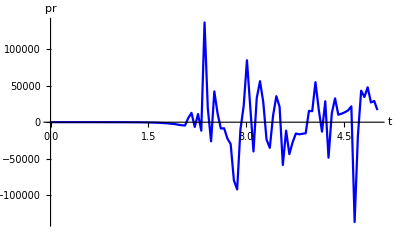

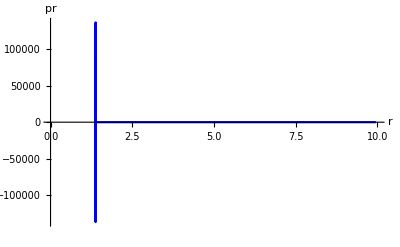

```mathematica
Block[
{dr,f,fr,r,l,rm,pr,t,q,qcrit,M,filter},
f[r1_,M1_,l1_]:=1-2M1/r1+r1^2/l1^2;
rm[l1_,r1_,q1_,M1_]:=NDSolveValue[{(4 l^6 M^3-4 l^6 M^2 r[t]+l^6 M r[t]^2-2 l^4 M r[t]^4+l^4 r[t]^5-3 l^2 M r[t]^6+2 l^2 r[t]^7+r[t]^9-3 l^6 M r[t]^2 r'[t]^2-3 l^4 r[t]^5 r'[t]^2-2 l^6 M q r[t] (1-(2 M)/r[t]+r[t]^2/l^2-r'[t]^2/(1-(2 M)/r[t]+r[t]^2/l^2))^(3/2)+l^6 q r[t]^2 (1-(2 M)/r[t]+r[t]^2/l^2-r'[t]^2/(1-(2 M)/r[t]+r[t]^2/l^2))^(3/2)+l^4 q r[t]^4 (1-(2 M)/r[t]+r[t]^2/l^2-r'[t]^2/(1-(2 M)/r[t]+r[t]^2/l^2))^(3/2)-2 l^6 M r[t]^3 r''[t]+l^6 r[t]^4 r''[t]+l^4 r[t]^6 r''[t])==0/.{l->l1,q->q1,M->M1},r[0]==r1,r'[0]==0},r,{t,0.01,5.01}];
qcrit[rs_,l1_,M1_]:=rs Sqrt[f[rs,M1,l1]];
fr[l1_,r1_,t1_,q1_,M1_]:=rm[l1,r1,q1,M1][t1];
dr[l1_,r1_,t1_,q1_,M1_]:=D[rm[l1,r1,q1,M1][t],t]/.{t->t1};
pr[l1_,r1_,t1_,q1_,M1_]:=dr[l1,r1,t1,q1,M1]/Sqrt[-dr[l1,r1,t1,q1,M1]^2f[fr[l1,r1,t1,q1,M1],M1,l1]+f[fr[l1,r1,t1,q1,M1],M1,l1]^3];
filter[x_]:=If[Im[x]==0,x,Abs[x]];
Print[
ListLinePlot[Table[{i,fr[1,10,i,0,2]//Re},{i,0.01,5.01,0.05}],PlotStyle->Blue,AxesLabel->{t,r},AxesOrigin->{0,0},PlotRange->{{0,5.01},{0,10}}]
];
Print[
ListLinePlot[Table[{i,filter[pr[1,10,i,0,2]]},{i,0.01,5.01,0.05}],PlotStyle->Blue,AxesLabel->{t,pr},AxesOrigin->{0,0},PlotRange->{{0,5.01},All}]
];
Print[
ListLinePlot[Table[{fr[1,10,i,0,2]//Re,pr[1,10,i,0,2]//filter},{i,0.01,5.01,0.05}],PlotStyle->Blue,AxesLabel->{r,pr},AxesOrigin->{0,0},PlotRange->{{0,10},All}]
]
]
```